```mathematica
mo=Import["/Users/victormanuelfreixaslemus/Desktop/Projects/Oxford_scattering/Benzene/vhf.out","Table"];
```

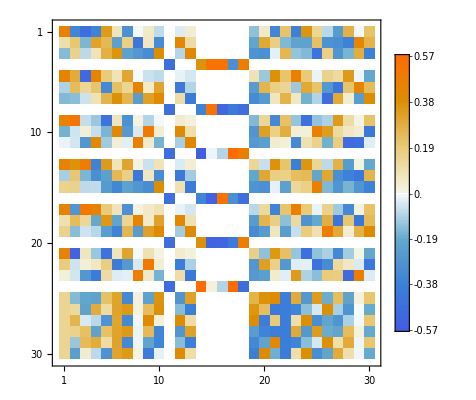

```mathematica
nbf=30;
nOcc=15;
moMatrix=Transpose[Partition[mo[[1,2;;]],nbf]];
MatrixPlot[moMatrix,PlotLegends->Automatic]
```

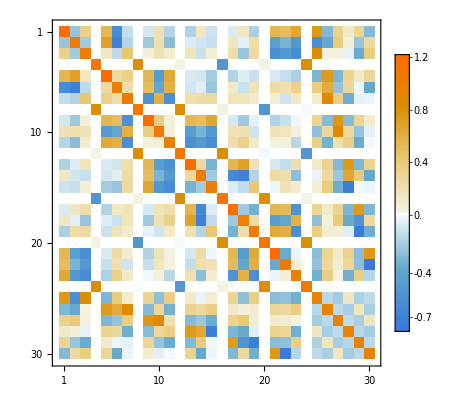

```mathematica
MatrixPlot[2moMatrix[[All,;;nOcc]].Transpose[moMatrix[[All,;;nOcc]]],PlotLegends->Automatic]
```

```mathematica
MatrixPlot[2moMatrix[[All,;;nOcc]].Transpose[moMatrix[[All,;;nOcc]]],PlotLegends->Automatic]
```

```mathematica
moMatrix.Transpose[moMatrix]//MatrixForm
```

(1. | 1.01824×10^-11 | 1.32756×10^-11 | 0. | -1.34414×10^-11 | 3.73348×10^-11 | -1.91761×10^-12 | 0. | -2.2932×10^-11 | -8.58868×10^-11 | -5.54317×10^-11 | 0. | -7.04395×10^-11 | -1.82588×10^-11 | 4.79255×10^-11 | 0. | -2.60418×10^-11 | -5.84976×10^-11 | -2.0352×10^-11 | 0. | 8.86047×10^-12 | 1.08591×10^-10 | 2.74176×10^-11 | 0. | 7.00622×10^-11 | 4.47194×10^-11 | -1.57933×10^-11 | -3.01681×10^-11 | 1.08718×10^-11 | -2.03453×10^-11
1.01824×10^-11 | 1. | 5.42185×10^-11 | 0. | 3.70178×10^-11 | -1.34752×10^-11 | 7.0359×10^-11 | 0. | 3.25584×10^-11 | -3.05835×10^-11 | 6.75628×10^-11 | 0. | -5.10267×10^-11 | -3.41209×10^-11 | -2.24207×10^-11 | 0. | -3.55513×10^-11 | 4.99125×10^-12 | 5.83196×10^-12 | 0. | 2.28895×10^-11 | 1.84118×10^-11 | 1.16313×10^-12 | 0. | 1.5993×10^-11 | -2.19044×10^-11 | 8.66152×10^-12 | 1.76187×10^-11 | 1.64983×10^-11 | -2.69708×10^-11
1.32756×10^-11 | 5.42185×10^-11 | 1. | 0. | -2.01877×10^-11 | 4.08245×10^-13 | 5.19028×10^-11 | 0. | 4.14261×10^-12 | 6.915×10^-12 | -7.0069×10^-11 | 0. | 8.46881×10^-12 | -6.03186×10^-11 | 7.46217×10^-11 | 0. | 3.95477×10^-11 | -3.34678×10^-11 | 7.72485×10^-11 | 0. | 3.43247×10^-11 | 2.58222×10^-11 | -6.39677×10^-11 | 0. | 5.7839×10^-11 | 1.22729×10^-11 | 8.36654×10^-12 | 7.07728×10^-11 | -1.17145×10^-11 | -2.45781×10^-11
0. | 0. | 0. | 1. | 0. | 0. | 0. | 1.97695×10^-11 | 0. | 0. | 0. | 6.59385×10^-11 | 0. | 0. | 0. | -6.79435×10^-11 | 0. | 0. | 0. | -5.07511×10^-11 | 0. | 0. | 0. | -4.01938×10^-12 | 0. | 0. | 0. | 0. | 0. | 0.
-1.34414×10^-11 | 3.70178×10^-11 | -2.01877×10^-11 | 0. | 1. | 2.45915×10^-11 | 7.31076×10^-12 | 0. | -1.19704×10^-10 | 2.60032×10^-12 | 2.41103×10^-11 | 0. | -5.2342×10^-11 | -3.30515×10^-11 | 3.34292×10^-11 | 0. | -3.58399×10^-11 | -6.02059×10^-11 | -6.86121×10^-11 | 0. | 6.21576×10^-11 | -5.93116×10^-11 | -5.46605×10^-11 | 0. | -2.92735×10^-11 | -7.73072×10^-11 | -1.03447×10^-11 | 3.29533×10^-11 | -6.74905×10^-12 | -2.9874×10^-11
3.73348×10^-11 | -1.34752×10^-11 | 4.08245×10^-13 | 0. | 2.45915×10^-11 | 1. | -2.38642×10^-11 | 0. | 7.35638×10^-12 | -4.04079×10^-11 | 3.02466×10^-11 | 0. | 7.47526×10^-11 | -6.2325×10^-11 | -1.70899×10^-11 | 0. | 4.45349×10^-11 | 2.19109×10^-12 | -7.15399×10^-11 | 0. | -5.22223×10^-11 | -6.74216×10^-12 | -6.90248×10^-11 | 0. | -6.49875×10^-11 | 3.57239×10^-12 | -9.0047×10^-12 | 2.66573×10^-12 | 5.75895×10^-11 | -6.58681×10^-12
-1.91761×10^-12 | 7.0359×10^-11 | 5.19028×10^-11 | 0. | 7.31076×10^-12 | -2.38642×10^-11 | 1. | 0. | -3.73865×10^-11 | 1.85322×10^-11 | 1.09085×10^-11 | 0. | -8.45272×10^-13 | 7.62356×10^-12 | 2.79561×10^-12 | 0. | 2.48697×10^-11 | -1.2956×10^-11 | 3.63549×10^-11 | 0. | -2.20615×10^-11 | -1.92967×10^-11 | 6.55331×10^-11 | 0. | -5.86087×10^-11 | 6.89573×10^-12 | 4.28209×10^-11 | -4.29745×10^-11 | -4.84862×10^-11 | 3.45829×10^-11
0. | 0. | 0. | 1.97695×10^-11 | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 2.50315×10^-11 | 0. | 0. | 0. | 1.8925×10^-11 | 0. | 0. | 0. | -8.57122×10^-11 | 0. | 0. | 0. | 6.8686×10^-11 | 0. | 0. | 0. | 0. | 0. | 0.
-2.2932×10^-11 | 3.25584×10^-11 | 4.14261×10^-12 | 0. | -1.19704×10^-10 | 7.35638×10^-12 | -3.73865×10^-11 | 0. | 1. | -5.20626×10^-11 | -2.65674×10^-11 | 0. | 3.95575×10^-11 | -3.20693×10^-11 | 2.11565×10^-11 | 0. | -2.65198×10^-11 | -5.53883×10^-11 | -4.68535×10^-11 | 0. | 7.30237×10^-11 | 4.53351×10^-11 | -8.76039×10^-12 | 0. | 3.55678×10^-11 | 4.58536×10^-11 | -2.27378×10^-11 | 9.27597×10^-12 | 9.64313×10^-12 | 7.85416×10^-12
-8.58868×10^-11 | -3.05835×10^-11 | 6.915×10^-12 | 0. | 2.60032×10^-12 | -4.04079×10^-11 | 1.85322×10^-11 | 0. | -5.20626×10^-11 | 1. | 5.08333×10^-11 | 0. | 8.42625×10^-11 | 5.52931×10^-11 | -4.63279×10^-11 | 0. | 2.76905×10^-11 | -2.90208×10^-11 | 2.03017×10^-11 | 0. | -7.23492×10^-11 | -2.51848×10^-12 | -1.39987×10^-11 | 0. | 8.09499×10^-11 | 1.78543×10^-11 | -6.19418×10^-11 | -3.55766×10^-11 | 1.45107×10^-11 | 6.9898×10^-13
-5.54317×10^-11 | 6.75628×10^-11 | -7.0069×10^-11 | 0. | 2.41103×10^-11 | 3.02466×10^-11 | 1.09085×10^-11 | 0. | -2.65674×10^-11 | 5.08333×10^-11 | 1. | 0. | 6.03813×10^-11 | -4.91965×10^-11 | -5.72658×10^-11 | 0. | 6.96995×10^-11 | 1.45467×10^-11 | -1.64538×10^-11 | 0. | -2.51202×10^-11 | -3.29951×10^-11 | 7.96104×10^-11 | 0. | 7.17132×10^-11 | 8.11855×10^-12 | -1.80134×10^-11 | 6.35962×10^-11 | -1.72183×10^-11 | -2.06094×10^-11
0. | 0. | 0. | 6.59385×10^-11 | 0. | 0. | 0. | 2.50315×10^-11 | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 7.2748×10^-11 | 0. | 0. | 0. | -1.89604×10^-12 | 0. | 0. | 0. | -1.23953×10^-11 | 0. | 0. | 0. | 0. | 0. | 0.
-7.04395×10^-11 | -5.10267×10^-11 | 8.46881×10^-12 | 0. | -5.2342×10^-11 | 7.47526×10^-11 | -8.45272×10^-13 | 0. | 3.95575×10^-11 | 8.42625×10^-11 | 6.03813×10^-11 | 0. | 1. | -9.3193×10^-12 | -2.5174×10^-11 | 0. | -5.38187×10^-11 | -4.02436×10^-11 | 4.09098×10^-11 | 0. | -1.09756×10^-10 | 1.68527×10^-11 | -4.89088×10^-11 | 0. | 1.1582×10^-11 | 3.68311×10^-11 | -3.70337×10^-11 | 1.51774×10^-11 | -1.96219×10^-11 | -4.21886×10^-11
-1.82588×10^-11 | -3.41209×10^-11 | -6.03186×10^-11 | 0. | -3.30515×10^-11 | -6.2325×10^-11 | 7.62356×10^-12 | 0. | -3.20693×10^-11 | 5.52931×10^-11 | -4.91965×10^-11 | 0. | -9.3193×10^-12 | 1. | 8.82756×10^-12 | 0. | 2.10072×10^-11 | -5.63662×10^-11 | -3.58149×10^-11 | 0. | -4.83301×10^-11 | -1.75342×10^-11 | 2.53962×10^-11 | 0. | 5.04538×10^-12 | -6.65242×10^-12 | 1.61403×10^-11 | -1.85188×10^-11 | 7.16887×10^-12 | 1.30508×10^-12
4.79255×10^-11 | -2.24207×10^-11 | 7.46217×10^-11 | 0. | 3.34292×10^-11 | -1.70899×10^-11 | 2.79561×10^-12 | 0. | 2.11565×10^-11 | -4.63279×10^-11 | -5.72658×10^-11 | 0. | -2.5174×10^-11 | 8.82756×10^-12 | 1. | 0. | -2.97827×10^-11 | 8.49857×10^-11 | 2.22876×10^-11 | 0. | 5.60819×10^-12 | -2.05831×10^-11 | -5.43171×10^-11 | 0. | -5.36565×10^-13 | -1.33229×10^-11 | 9.86512×10^-12 | -3.39812×10^-11 | -1.84023×10^-11 | -7.81453×10^-12
0. | 0. | 0. | -6.79435×10^-11 | 0. | 0. | 0. | 1.8925×10^-11 | 0. | 0. | 0. | 7.2748×10^-11 | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 7.2053×10^-12 | 0. | 0. | 0. | -2.70526×10^-12 | 0. | 0. | 0. | 0. | 0. | 0.
-2.60418×10^-11 | -3.55513×10^-11 | 3.95477×10^-11 | 0. | -3.58399×10^-11 | 4.45349×10^-11 | 2.48697×10^-11 | 0. | -2.65198×10^-11 | 2.76905×10^-11 | 6.96995×10^-11 | 0. | -5.38187×10^-11 | 2.10072×10^-11 | -2.97827×10^-11 | 0. | 1. | 4.90084×10^-12 | -1.05892×10^-11 | 0. | 2.8732×10^-11 | -1.11166×10^-12 | -5.84441×10^-11 | 0. | -1.08035×10^-11 | -1.63175×10^-11 | 7.13274×10^-11 | 5.81655×10^-11 | -4.60818×10^-11 | 2.39512×10^-11
-5.84976×10^-11 | 4.99125×10^-12 | -3.34678×10^-11 | 0. | -6.02059×10^-11 | 2.19109×10^-12 | -1.2956×10^-11 | 0. | -5.53883×10^-11 | -2.90208×10^-11 | 1.45467×10^-11 | 0. | -4.02436×10^-11 | -5.63662×10^-11 | 8.49857×10^-11 | 0. | 4.90084×10^-12 | 1. | -2.6886×10^-11 | 0. | 3.8875×10^-11 | -9.07889×10^-11 | -4.71583×10^-11 | 0. | -2.72438×10^-11 | -6.48974×10^-11 | 3.26263×10^-11 | -2.32992×10^-11 | -1.92357×10^-11 | -1.59149×10^-11
-2.0352×10^-11 | 5.83196×10^-12 | 7.72485×10^-11 | 0. | -6.86121×10^-11 | -7.15399×10^-11 | 3.63549×10^-11 | 0. | -4.68535×10^-11 | 2.03017×10^-11 | -1.64538×10^-11 | 0. | 4.09098×10^-11 | -3.58149×10^-11 | 2.22876×10^-11 | 0. | -1.05892×10^-11 | -2.6886×10^-11 | 1. | 0. | 3.81772×10^-11 | 2.15313×10^-11 | 3.19881×10^-12 | 0. | -2.77196×10^-11 | -4.06837×10^-12 | 1.16774×10^-11 | -7.57349×10^-14 | 1.10717×10^-11 | 6.03513×10^-11
0. | 0. | 0. | -5.07511×10^-11 | 0. | 0. | 0. | -8.57122×10^-11 | 0. | 0. | 0. | -1.89604×10^-12 | 0. | 0. | 0. | 7.2053×10^-12 | 0. | 0. | 0. | 1. | 0. | 0. | 0. | -2.11876×10^-11 | 0. | 0. | 0. | 0. | 0. | 0.
8.86047×10^-12 | 2.28895×10^-11 | 3.43247×10^-11 | 0. | 6.21576×10^-11 | -5.22223×10^-11 | -2.20615×10^-11 | 0. | 7.30237×10^-11 | -7.23492×10^-11 | -2.51202×10^-11 | 0. | -1.09756×10^-10 | -4.83301×10^-11 | 5.60819×10^-12 | 0. | 2.8732×10^-11 | 3.8875×10^-11 | 3.81772×10^-11 | 0. | 1. | -2.16884×10^-11 | -3.23191×10^-11 | 0. | -1.99595×10^-11 | 5.4884×10^-12 | -1.72493×10^-11 | -2.43464×10^-11 | 5.52149×10^-11 | -2.14355×10^-11
1.08591×10^-10 | 1.84118×10^-11 | 2.58222×10^-11 | 0. | -5.93116×10^-11 | -6.74216×10^-12 | -1.92967×10^-11 | 0. | 4.53351×10^-11 | -2.51848×10^-12 | -3.29951×10^-11 | 0. | 1.68527×10^-11 | -1.75342×10^-11 | -2.05831×10^-11 | 0. | -1.11166×10^-12 | -9.07889×10^-11 | 2.15313×10^-11 | 0. | -2.16884×10^-11 | 1. | 2.83561×10^-12 | 0. | 2.23258×10^-11 | 5.46732×10^-11 | 5.03831×10^-11 | 1.32677×10^-11 | -4.8197×10^-11 | 4.89963×10^-11
2.74176×10^-11 | 1.16313×10^-12 | -6.39677×10^-11 | 0. | -5.46605×10^-11 | -6.90248×10^-11 | 6.55331×10^-11 | 0. | -8.76039×10^-12 | -1.39987×10^-11 | 7.96104×10^-11 | 0. | -4.89088×10^-11 | 2.53962×10^-11 | -5.43171×10^-11 | 0. | -5.84441×10^-11 | -4.71583×10^-11 | 3.19881×10^-12 | 0. | -3.23191×10^-11 | 2.83561×10^-12 | 1. | 0. | -4.34882×10^-11 | 5.63698×10^-11 | 3.73775×10^-11 | 1.33495×10^-11 | 2.82758×10^-12 | 6.02283×10^-12
0. | 0. | 0. | -4.01938×10^-12 | 0. | 0. | 0. | 6.8686×10^-11 | 0. | 0. | 0. | -1.23953×10^-11 | 0. | 0. | 0. | -2.70526×10^-12 | 0. | 0. | 0. | -2.11876×10^-11 | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
7.00622×10^-11 | 1.5993×10^-11 | 5.7839×10^-11 | 0. | -2.92735×10^-11 | -6.49875×10^-11 | -5.86087×10^-11 | 0. | 3.55678×10^-11 | 8.09499×10^-11 | 7.17132×10^-11 | 0. | 1.1582×10^-11 | 5.04538×10^-12 | -5.36565×10^-13 | 0. | -1.08035×10^-11 | -2.72438×10^-11 | -2.77196×10^-11 | 0. | -1.99595×10^-11 | 2.23258×10^-11 | -4.34882×10^-11 | 0. | 1. | -1.81992×10^-11 | 2.67215×10^-11 | 7.39952×10^-11 | 4.573×10^-11 | 1.06387×10^-11
4.47194×10^-11 | -2.19044×10^-11 | 1.22729×10^-11 | 0. | -7.73072×10^-11 | 3.57239×10^-12 | 6.89573×10^-12 | 0. | 4.58536×10^-11 | 1.78543×10^-11 | 8.11855×10^-12 | 0. | 3.68311×10^-11 | -6.65242×10^-12 | -1.33229×10^-11 | 0. | -1.63175×10^-11 | -6.48974×10^-11 | -4.06837×10^-12 | 0. | 5.4884×10^-12 | 5.46732×10^-11 | 5.63698×10^-11 | 0. | -1.81992×10^-11 | 1. | 5.55947×10^-11 | -8.53812×10^-12 | -2.14087×10^-11 | -6.61359×10^-12
-1.57933×10^-11 | 8.66152×10^-12 | 8.36654×10^-12 | 0. | -1.03447×10^-11 | -9.0047×10^-12 | 4.28209×10^-11 | 0. | -2.27378×10^-11 | -6.19418×10^-11 | -1.80134×10^-11 | 0. | -3.70337×10^-11 | 1.61403×10^-11 | 9.86512×10^-12 | 0. | 7.13274×10^-11 | 3.26263×10^-11 | 1.16774×10^-11 | 0. | -1.72493×10^-11 | 5.03831×10^-11 | 3.73775×10^-11 | 0. | 2.67215×10^-11 | 5.55947×10^-11 | 1. | 4.01286×10^-11 | -7.00106×10^-11 | 8.13855×10^-12
-3.01681×10^-11 | 1.76187×10^-11 | 7.07728×10^-11 | 0. | 3.29533×10^-11 | 2.66573×10^-12 | -4.29745×10^-11 | 0. | 9.27597×10^-12 | -3.55766×10^-11 | 6.35962×10^-11 | 0. | 1.51774×10^-11 | -1.85188×10^-11 | -3.39812×10^-11 | 0. | 5.81655×10^-11 | -2.32992×10^-11 | -7.57349×10^-14 | 0. | -2.43464×10^-11 | 1.32677×10^-11 | 1.33495×10^-11 | 0. | 7.39952×10^-11 | -8.53812×10^-12 | 4.01286×10^-11 | 1. | 2.78904×10^-11 | -6.69106×10^-11
1.08718×10^-11 | 1.64983×10^-11 | -1.17145×10^-11 | 0. | -6.74905×10^-12 | 5.75895×10^-11 | -4.84862×10^-11 | 0. | 9.64313×10^-12 | 1.45107×10^-11 | -1.72183×10^-11 | 0. | -1.96219×10^-11 | 7.16887×10^-12 | -1.84023×10^-11 | 0. | -4.60818×10^-11 | -1.92357×10^-11 | 1.10717×10^-11 | 0. | 5.52149×10^-11 | -4.8197×10^-11 | 2.82758×10^-12 | 0. | 4.573×10^-11 | -2.14087×10^-11 | -7.00106×10^-11 | 2.78904×10^-11 | 1. | -9.00602×10^-12
-2.03453×10^-11 | -2.69708×10^-11 | -2.45781×10^-11 | 0. | -2.9874×10^-11 | -6.58681×10^-12 | 3.45829×10^-11 | 0. | 7.85416×10^-12 | 6.9898×10^-13 | -2.06094×10^-11 | 0. | -4.21886×10^-11 | 1.30508×10^-12 | -7.81453×10^-12 | 0. | 2.39512×10^-11 | -1.59149×10^-11 | 6.03513×10^-11 | 0. | -2.14355×10^-11 | 4.89963×10^-11 | 6.02283×10^-12 | 0. | 1.06387×10^-11 | -6.61359×10^-12 | 8.13855×10^-12 | -6.69106×10^-11 | -9.00602×10^-12 | 1.)

```mathematica
moMatrix[[All,;;nOcc]].Transpose[moMatrix[[All,;;nOcc]]]//MatrixForm
```

(0.609295 | -0.0172751 | 0.027989 | 0. | 0.142571 | -0.240083 | -0.00939391 | 0. | -0.00587578 | 0.00942778 | -0.0124837 | 0. | -0.0128479 | 0.00453653 | -0.00731866 | 0. | -0.00582383 | 0.00695331 | -0.0139299 | 0. | 0.142409 | 0.11522 | 0.210786 | 0. | 0.279031 | -0.0238447 | 0.0238123 | 0.00300685 | 0.0237853 | -0.0238355
-0.0172751 | 0.470298 | -0.0150984 | 0. | 0.240102 | -0.321789 | -0.0125565 | 0. | -0.0156114 | 0.0126421 | -0.0237453 | 0. | -0.00455294 | -0.00708392 | -0.00832972 | 0. | 0.0060698 | -0.00207364 | 0.0152252 | 0. | -0.111908 | -0.0258289 | -0.158486 | 0. | -0.210635 | -0.0356943 | 0.0369534 | 0.00107215 | -0.0171187 | 0.0157163
0.027989 | -0.0150984 | 0.485492 | 0. | 0.00575659 | -0.0115169 | 0.059131 | 0. | 0.00094401 | 0.00790425 | 0.00212291 | 0. | 0.0073065 | -0.00831463 | 0.00119518 | 0. | 0.0143464 | -0.0164152 | 0.0168449 | 0. | -0.212524 | -0.159609 | -0.236999 | 0. | 0.339493 | 0.00018708 | 0.000811999 | -0.00170333 | -0.032699 | 0.0320402
0. | 0. | 0. | 0.500012 | 0. | 0. | 0. | 0.333235 | 0. | 0. | 0. | 1.84193×10^-6 | 0. | 0. | 0. | -0.16674 | 0. | 0. | 0. | 3.89671×10^-6 | 0. | 0. | 0. | 0.333394 | 0. | 0. | 0. | 0. | 0. | 0.
0.142571 | 0.240102 | 0.00575659 | 0. | 0.609252 | 0.0155432 | 0.0290048 | 0. | 0.142554 | -0.128087 | 0.203273 | 0. | -0.00583472 | -0.00607946 | -0.0143659 | 0. | -0.0128233 | -0.00406479 | -0.00756719 | 0. | -0.00584607 | -0.00863989 | -0.0130319 | 0. | -0.0238973 | 0.279012 | -0.0238959 | 0.0237927 | 0.00299605 | 0.0237904
-0.240083 | -0.321789 | -0.0115169 | 0. | 0.0155432 | 0.468435 | 0.0140825 | 0. | 0.125116 | -0.0464301 | 0.170538 | 0. | -0.00696383 | -0.00208158 | -0.0164354 | 0. | 0.00407155 | -0.00805965 | 0.00772143 | 0. | 0.0154997 | 0.0116589 | 0.0243407 | 0. | 0.0356831 | 0.188677 | -0.0177756 | 0.0191349 | -0.000960478 | -0.036908
-0.00939391 | -0.0125565 | 0.059131 | 0. | 0.0290048 | 0.0140825 | 0.48727 | 0. | -0.205068 | 0.171353 | -0.216196 | 0. | 0.0139164 | 0.0152191 | 0.0168264 | 0. | 0.00756433 | 0.0077089 | 0.00220099 | 0. | 0.0019348 | -0.00728173 | 0.00318086 | 0. | 0.00239262 | 0.352186 | 0.031038 | -0.031527 | -0.00176071 | -0.00152387
0. | 0. | 0. | 0.333235 | 0. | 0. | 0. | 0.499996 | 0. | 0. | 0. | 0.333401 | 0. | 0. | 0. | 4.13354×10^-6 | 0. | 0. | 0. | -0.166727 | 0. | 0. | 0. | -5.84291×10^-6 | 0. | 0. | 0. | 0. | 0. | 0.
-0.00587578 | -0.0156114 | 0.00094401 | 0. | 0.142554 | 0.125116 | -0.205068 | 0. | 0.609329 | 0.033015 | 0.0010405 | 0. | 0.142397 | 0.11189 | 0.21251 | 0. | -0.00585388 | -0.0154889 | -0.00191822 | 0. | -0.0128303 | -0.00860779 | -0.000260566 | 0. | 0.0237928 | -0.0237913 | 0.279112 | -0.0237675 | 0.023781 | 0.00297455
0.00942778 | 0.0126421 | 0.00790425 | 0. | -0.128087 | -0.0464301 | 0.171353 | 0. | 0.033015 | 0.49471 | 0.00108771 | 0. | -0.115257 | -0.0258643 | -0.159651 | 0. | 0.0086556 | 0.0116632 | -0.00729709 | 0. | 0.00860971 | 0.00637877 | 0.000575211 | 0. | -0.0197438 | 0.0198866 | 0.399242 | 0.0180115 | -0.0177957 | -0.00198504
-0.0124837 | -0.0237453 | 0.00212291 | 0. | 0.203273 | 0.170538 | -0.216196 | 0. | 0.0010405 | 0.00108771 | 0.461076 | 0. | -0.210776 | -0.158458 | -0.236986 | 0. | 0.0130493 | 0.0243355 | 0.00315762 | 0. | 0.000277327 | 0.000589656 | -0.0121992 | 0. | 0.0311963 | -0.0296422 | 0.0122506 | 0.0307529 | -0.032369 | -0.0000676226
0. | 0. | 0. | 1.84193×10^-6 | 0. | 0. | 0. | 0.333401 | 0. | 0. | 0. | 0.499992 | 0. | 0. | 0. | 0.333333 | 0. | 0. | 0. | -6.01648×10^-6 | 0. | 0. | 0. | -0.166532 | 0. | 0. | 0. | 0. | 0. | 0.
-0.0128479 | -0.00455294 | 0.0073065 | 0. | -0.00583472 | -0.00696383 | 0.0139164 | 0. | 0.142397 | -0.115257 | -0.210776 | 0. | 0.609298 | 0.0173139 | -0.0279804 | 0. | 0.14262 | 0.240048 | 0.00928921 | 0. | -0.0058727 | -0.00943251 | 0.0124845 | 0. | 0.0030049 | 0.0237942 | -0.0238401 | 0.279033 | -0.023873 | 0.0238055
0.00453653 | -0.00708392 | -0.00831463 | 0. | -0.00607946 | -0.00208158 | 0.0152191 | 0. | 0.11189 | -0.0258643 | -0.158458 | 0. | 0.0173139 | 0.470264 | -0.015106 | 0. | -0.240168 | -0.321748 | -0.0124062 | 0. | 0.0156036 | 0.0126496 | -0.0237418 | 0. | -0.00106528 | 0.0171185 | -0.0156987 | 0.210644 | 0.035748 | -0.0369439
-0.00731866 | -0.00832972 | 0.00119518 | 0. | -0.0143659 | -0.0164354 | 0.0168264 | 0. | 0.21251 | -0.159651 | -0.236986 | 0. | -0.0279804 | -0.015106 | 0.485484 | 0. | -0.00576643 | -0.0115047 | 0.0591621 | 0. | -0.000944648 | 0.00790382 | 0.00212239 | 0. | 0.00170644 | 0.0327185 | -0.0320404 | -0.339483 | -0.000152037 | -0.000815407
0. | 0. | 0. | -0.16674 | 0. | 0. | 0. | 4.13354×10^-6 | 0. | 0. | 0. | 0.333333 | 0. | 0. | 0. | 0.500012 | 0. | 0. | 0. | 0.333297 | 0. | 0. | 0. | 1.9949×10^-6 | 0. | 0. | 0. | 0. | 0. | 0.
-0.00582383 | 0.0060698 | 0.0143464 | 0. | -0.0128233 | 0.00407155 | 0.00756433 | 0. | -0.00585388 | 0.0086556 | 0.0130493 | 0. | 0.14262 | -0.240168 | -0.00576643 | 0. | 0.609251 | -0.0155023 | -0.029022 | 0. | 0.142493 | 0.128086 | -0.203208 | 0. | 0.0237865 | 0.00299686 | 0.0237956 | -0.0238961 | 0.27901 | -0.0238845
0.00695331 | -0.00207364 | -0.0164152 | 0. | -0.00406479 | -0.00805965 | 0.0077089 | 0. | -0.0154889 | 0.0116632 | 0.0243355 | 0. | 0.240048 | -0.321748 | -0.0115047 | 0. | -0.0155023 | 0.46843 | 0.0140683 | 0. | -0.12504 | -0.0464151 | 0.170445 | 0. | -0.0191219 | 0.000957266 | 0.0368913 | -0.0356833 | -0.188944 | 0.0177551
-0.0139299 | 0.0152252 | 0.0168449 | 0. | -0.00756719 | 0.00772143 | 0.00220099 | 0. | -0.00191822 | -0.00729709 | 0.00315762 | 0. | 0.00928921 | -0.0124062 | 0.0591621 | 0. | -0.029022 | 0.0140683 | 0.487291 | 0. | 0.205141 | 0.171424 | -0.216299 | 0. | 0.0315516 | 0.0017629 | 0.00149695 | -0.00238631 | -0.352046 | -0.0310292
0. | 0. | 0. | 3.89671×10^-6 | 0. | 0. | 0. | -0.166727 | 0. | 0. | 0. | -6.01648×10^-6 | 0. | 0. | 0. | 0.333297 | 0. | 0. | 0. | 0.499996 | 0. | 0. | 0. | 0.333339 | 0. | 0. | 0. | 0. | 0. | 0.
0.142409 | -0.111908 | -0.212524 | 0. | -0.00584607 | 0.0154997 | 0.0019348 | 0. | -0.0128303 | 0.00860971 | 0.000277327 | 0. | -0.0058727 | 0.0156036 | -0.000944648 | 0. | 0.142493 | -0.12504 | 0.205141 | 0. | 0.609324 | -0.032996 | -0.00105465 | 0. | -0.0237549 | 0.023775 | 0.00297721 | 0.0237959 | -0.0237588 | 0.279108
0.11522 | -0.0258289 | -0.159609 | 0. | -0.00863989 | 0.0116589 | -0.00728173 | 0. | -0.00860779 | 0.00637877 | 0.000589656 | 0. | -0.00943251 | 0.0126496 | 0.00790382 | 0. | 0.128086 | -0.0464151 | 0.171424 | 0. | -0.032996 | 0.494723 | 0.00107566 | 0. | -0.018001 | 0.0177721 | 0.00198653 | 0.019755 | -0.0198841 | -0.399247
0.210786 | -0.158486 | -0.236999 | 0. | -0.0130319 | 0.0243407 | 0.00318086 | 0. | -0.000260566 | 0.000575211 | -0.0121992 | 0. | 0.0124845 | -0.0237418 | 0.00212239 | 0. | -0.203208 | 0.170445 | -0.216299 | 0. | -0.00105465 | 0.00107566 | 0.461122 | 0. | -0.0307509 | 0.0323589 | 0.000061226 | -0.0311996 | 0.029576 | -0.0123448
0. | 0. | 0. | 0.333394 | 0. | 0. | 0. | -5.84291×10^-6 | 0. | 0. | 0. | -0.166532 | 0. | 0. | 0. | 1.9949×10^-6 | 0. | 0. | 0. | 0.333339 | 0. | 0. | 0. | 0.499992 | 0. | 0. | 0. | 0. | 0. | 0.
0.279031 | -0.210635 | 0.339493 | 0. | -0.0238973 | 0.0356831 | 0.00239262 | 0. | 0.0237928 | -0.0197438 | 0.0311963 | 0. | 0.0030049 | -0.00106528 | 0.00170644 | 0. | 0.0237865 | -0.0191219 | 0.0315516 | 0. | -0.0237549 | -0.018001 | -0.0307509 | 0. | 0.434987 | -0.0120453 | -0.0141735 | 0.00696104 | -0.0141455 | -0.0120126
-0.0238447 | -0.0356943 | 0.00018708 | 0. | 0.279012 | 0.188677 | 0.352186 | 0. | -0.0237913 | 0.0198866 | -0.0296422 | 0. | 0.0237942 | 0.0171185 | 0.0327185 | 0. | 0.00299686 | 0.000957266 | 0.0017629 | 0. | 0.023775 | 0.0177721 | 0.0323589 | 0. | -0.0120453 | 0.434995 | -0.0120202 | -0.0141557 | 0.00696676 | -0.014147
0.0238123 | 0.0369534 | 0.000811999 | 0. | -0.0238959 | -0.0177756 | 0.031038 | 0. | 0.279112 | 0.399242 | 0.0122506 | 0. | -0.0238401 | -0.0156987 | -0.0320404 | 0. | 0.0237956 | 0.0368913 | 0.00149695 | 0. | 0.00297721 | 0.00198653 | 0.000061226 | 0. | -0.0141735 | -0.0120202 | 0.434841 | -0.0120064 | -0.0141546 | 0.00700587
0.00300685 | 0.00107215 | -0.00170333 | 0. | 0.0237927 | 0.0191349 | -0.031527 | 0. | -0.0237675 | 0.0180115 | 0.0307529 | 0. | 0.279033 | 0.210644 | -0.339483 | 0. | -0.0238961 | -0.0356833 | -0.00238631 | 0. | 0.0237959 | 0.019755 | -0.0311996 | 0. | 0.00696104 | -0.0141557 | -0.0120064 | 0.434977 | -0.0120457 | -0.0141707
0.0237853 | -0.0171187 | -0.032699 | 0. | 0.00299605 | -0.000960478 | -0.00176071 | 0. | 0.023781 | -0.0177957 | -0.032369 | 0. | -0.023873 | 0.035748 | -0.000152037 | 0. | 0.27901 | -0.188944 | -0.352046 | 0. | -0.0237588 | -0.0198841 | 0.029576 | 0. | -0.0141455 | 0.00696676 | -0.0141546 | -0.0120457 | 0.434998 | -0.0120229
-0.0238355 | 0.0157163 | 0.0320402 | 0. | 0.0237904 | -0.036908 | -0.00152387 | 0. | 0.00297455 | -0.00198504 | -0.0000676226 | 0. | 0.0238055 | -0.0369439 | -0.000815407 | 0. | -0.0238845 | 0.0177551 | -0.0310292 | 0. | 0.279108 | -0.399247 | -0.0123448 | 0. | -0.0120126 | -0.014147 | 0.00700587 | -0.0141707 | -0.0120229 | 0.434857)